## CellzillaModelToXML Example File

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (0.15-α (19-Jun-09)) loaded Sat 20 Jun 2009 11:30:49 using xlr8r 0.74 (13 May 2009)

```mathematica
<<xlr8r.m
```

```mathematica
<<CelleratorML.m
```

Generate a Cellzilla Model from Random Centers and convert the centers to a Tissue object

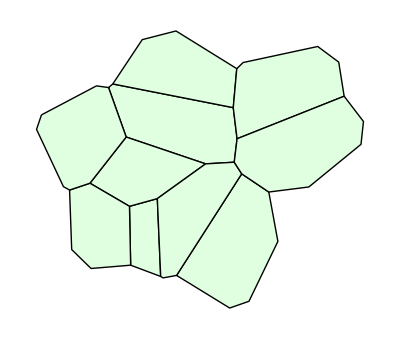

```mathematica
n=10; 
r:= RandomReal[{0, 10}]; 
centers=Table[{r,r}, {n}];
w=BoundedCellVoronoi[centers];
ShowTissue[w]
```

Define a Cellerator Model and save it to the xml file ring.xml

```mathematica
reactions={{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
{Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};
cic= {X-> 1, Y-> 2, Z-> 3};
cparms={v-> 1, K-> .5};
```

```mathematica
SaveModel["ring.xml" , reactions, "InitialConditions"-> cic, "Parmaters"-> cparms]
```

ring.xml

Define the Cellzilla Network on this template

```mathematica
bignet=CelleratorNetwork[reactions, {{X, DX}, {Y, DY}, {Z, DZ}}, w];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

108 diffusion reactions.

168 total reactions.

Define Random Initial Conditions

```mathematica
myic=ListICToCellzillaIC[{X-> Table[RandomReal[{0,3}], {n}], Y-> Table[RandomReal[{0,3}], {n}], Z-> Table[RandomReal[{0,3}], {n}], XP-> Table[0, {n}], YP-> Table[0, {n}], ZP-> Table[0, {n}]}];
```

Generate the Symbolic XML using CellzillaModelToSXML

```mathematica
xml=CellzillaModelToXML[
"Models"-> {"ring.xml"},
"Tissue"-> w, 
"Parameters"-> {DX-> 9, DY-> 10, DZ-> 11},
"InitialConditions"-> myic,
"DiffusingSpecies"-> {{X,DX}, {Y,DY}, {Z,DZ}}];
```

Model name: CellzillaModel

Model file name(s) or URL(s):

ring.xml

3 Diffusing Species

3 Parameters

60 Initial Conditions

2-D tissue: 36 vertices; 45 edges; 10 cells.

```mathematica
Short[xml,25]
```

<CellzillaModel Name='CellzillaModel'>
 <ListOfCelleratorModels>
  <CelleratorModel>ring.xml</CelleratorModel>
 </ListOfCelleratorModels>
 <ListOfDiffusingSpecies>
  <DiffusingSpecies Identifier='X'
      Rate='DX' />
  <DiffusingSpecies Identifier='Y'
      Rate='DY' />
  <DiffusingSpecies Identifier='Z'
      Rate='DZ' />
 </ListOfDiffusingSpecies>
 <ListOfCellzillaParameters>
  <Parameter Identifier='DX'
      Value='9' />
  <Parameter Identifier='DY'
      Value='10' />
  <Parameter Identifier='DZ'
      Value='11' />
 </ListOfCellzillaParameters>
 <ListOfCellzillaIC>
  <CellzillaIC Identifier='X'>
   <math xmlns='http://www.w3.org/1998/Math/MathML'>
    <list>
     <cn type='real'>1.3243887320625731</cn>
     <cn type='real'>2.9603247094077956</cn>
     <cn type='real'>2.8719791513463697</cn>
     <cn type='real'>2.6632907043966236</cn>
     <cn type='real'>2.48138346163938</cn>
     <cn type='real'>2.5366649682430698</cn>
     <cn t…ger'>6</cn>
      <cn type='integer'>8</cn>
      <cn type='integer'>13</cn>
      <cn type='integer'>11</cn>
     </list>
     <list>
      <cn type='integer'>26</cn>
      <cn type='integer'>29</cn>
      <cn type='integer'>38</cn>
      <cn type='integer'>39</cn>
      <cn type='integer'>36</cn>
      <cn type='integer'>27</cn>
     </list>
     <list>
      <cn type='integer'>22</cn>
      <cn type='integer'>21</cn>
      <cn type='integer'>23</cn>
      <cn type='integer'>24</cn>
      <cn type='integer'>27</cn>
      <cn type='integer'>33</cn>
      <cn type='integer'>28</cn>
     </list>
     <list>
      <cn type='integer'>32</cn>
      <cn type='integer'>33</cn>
      <cn type='integer'>36</cn>
      <cn type='integer'>40</cn>
      <cn type='integer'>41</cn>
      <cn type='integer'>45</cn>
      <cn type='integer'>44</cn>
      <cn type='integer'>35</cn>
     </list>
    </list>
   </math>
  </Cells>
 </Tissue>
</CellzillaModel>